# Midterm Exam

```mathematica
img = -Graphics-;
```

```mathematica
f[x_]  := Piecewise[ {
{Sqrt[-x],  x ≤ 0},
{Sqrt[x],  0 ≤ x}
}];
```

```mathematica
xi = {-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}
fxi = {.5,2,2,2.33,2,2.75,2.75,2.75,2.6,2.75,2.33,2.25,1.9,1.6,1.4,1.2,1,0,.75,1,1.3,1.5,1.6,1.75,2.25,2.25,2.6,2.6,2.6,2.6,2.6,2.25,2,1.6,1.5,1.75}
```

{-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}

{0.5,2,2,2.33,2,2.75,2.75,2.75,2.6,2.75,2.33,2.25,1.9,1.6,1.4,1.2,1,0,0.75,1,1.3,1.5,1.6,1.75,2.25,2.25,2.6,2.6,2.6,2.6,2.6,2.25,2,1.6,1.5,1.75}

```mathematica
n = Length[xi]
l =4;
m = Length[xi]/l;
OrderedPairs = Table[{}, n];
For[ i=1, i ≤ n, i++,
OrderedPairs[[i]] = {xi[[i]],fxi[[i]]}
]
OrderedPairs
```

36

{{-17,0.5},{-16,2},{-15,2},{-14,2.33},{-13,2},{-12,2.75},{-11,2.75},{-10,2.75},{-9,2.6},{-8,2.75},{-7,2.33},{-6,2.25},{-5,1.9},{-4,1.6},{-3,1.4},{-2,1.2},{-1,1},{0,0},{1,0.75},{2,1},{3,1.3},{4,1.5},{5,1.6},{6,1.75},{7,2.25},{8,2.25},{9,2.6},{10,2.6},{11,2.6},{12,2.6},{13,2.6},{14,2.25},{15,2},{16,1.6},{17,1.5},{18,1.75}}

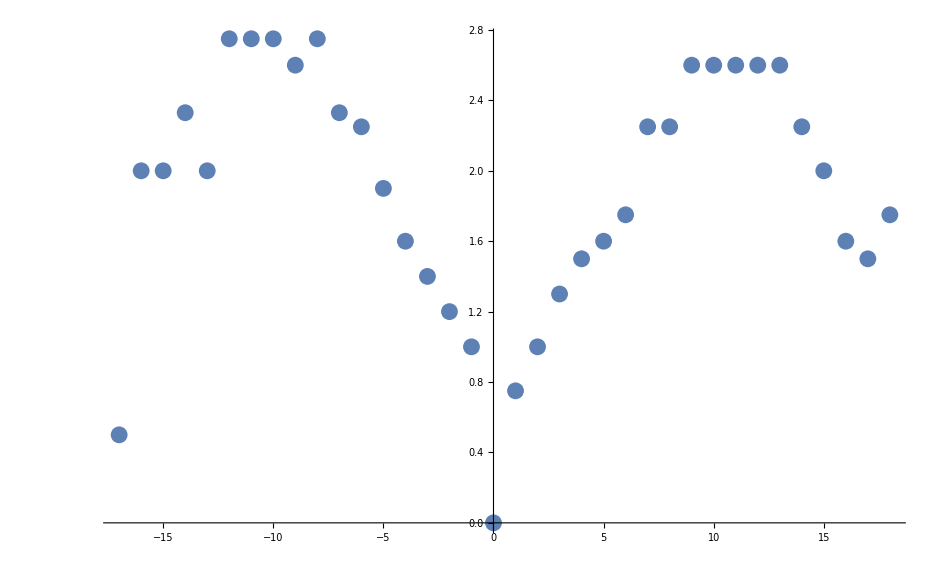

```mathematica
ListPlot[OrderedPairs]
```

## Lagrange Interpolation:

```mathematica
MatrixForm[DivDif=Table[{},m,m]];
For[i=1,i≤m,i++,DivDif[[i,1]]=fxi[[l*i]]] ;
MatrixForm[DivDif];
For[j=2,j≤m,j++,
For[i=j,i≤m,i++,DivDif[[i,j]]=
(DivDif[[i,j-1]]-DivDif[[i-1,j-1]])/ 
(xi[[i]]-xi[[i-(j-1)]])]]
MatrixForm[DivDif];
Lag[x_]:=Sum[DivDif[[i,i]]*Product[(x-xi[[l*j]]),{j,1,i-1}],{i,1,m}]
Simplify[Lag[x]]
```

636.79+109.47 x-143.206 x^2-9.65522 x^3+4.48253 x^4+0.140194 x^5-0.0423056 x^6-0.000501984 x^7+0.000116071 x^8

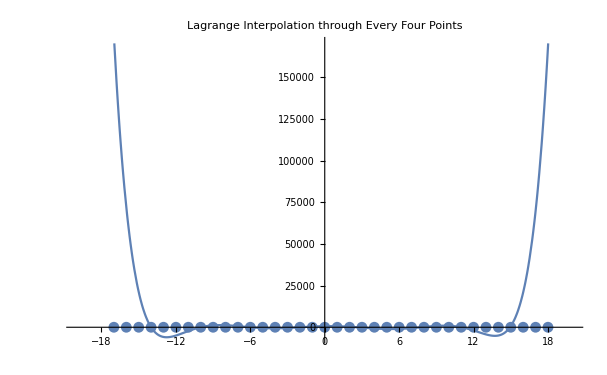

```mathematica
Show[
Plot[Lag[x],{x,-20,20}, PlotLabel-> "Lagrange Interpolation through Every Four Points"],
ListPlot[OrderedPairs]
]
```

## Numerical Differentiation

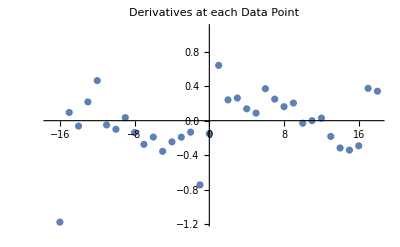

```mathematica
h=xi[[2]]-xi[[1]];
derivfxi=Table[{},n];
For[i=3,i≤n-2,i++,                  
derivfxi[[i]]=
(fxi[[i-2]]-8fxi[[i-1]]+
8fxi[[i+1]]-fxi[[i+2]])/(12h)]
For[i=1,i≤2,i++, 
derivfxi[[i]]=
(−25fxi[[i]]+48fxi[[i+1]]−36fxi[[i+2]]+
16fxi[[i+3]]−3fxi[[i+4]])(1/(12h))]
For[i=n,i≥n-1,i--, 
derivfxi[[i]]=
(−25fxi[[i]]+48fxi[[i-1]]−36fxi[[i-2]]+
16fxi[[i-3]]−3fxi[[i-4]])(1/(12(-h)))]
derivfxi;
OrderedPairs2 = Table[{}, n];
For[ i=1, i ≤ n, i++,
OrderedPairs2[[i]] = {xi[[i]],derivfxi[[i]]}
];
OrderedPairs2;
ListPlot[OrderedPairs2, PlotLabel->"Derivatives at each Data Point"]
```

## Hermite Interpolation

```mathematica
q = 4;
w=2*Length[xi]/q;
MatrixForm[DivDif2=Table[{},w,w+1]];
For[i=1,i≤w/2,i++,
DivDif2[[(2 i),1]]=xi[[q*i]]] 
For[i=1,i≤w/2,i++,
DivDif2[[(2i)-1,1]]=xi[[q*i]]]

 MatrixForm[DivDif2];

For[i=1,i≤w / 2,i++,
DivDif2[[(2i),2]]=fxi[[q*i]]]
For[i=1,i≤w/2,i++,
DivDif2[[(2i)-1,2]]=fxi[[q*i]]]

MatrixForm[DivDif2];

For[ j=2,j≤2,j++,
For[i=j,i≤w,i++,DivDif2[[i,j+1]]=(DivDif2[[i,j]]-DivDif2[[i-1,j]]) / 
(DivDif2[[i,j-1]]-DivDif2[[i-1,j-1]])
]] 
MatrixForm[DivDif2];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
For[i=1,i≤w/2,i++,
DivDif2[[(2i),3]]=derivfxi[[q*i]]]
MatrixForm[DivDif2];
For[ j=3,j≤w,j++,
For[i=j,i≤w,i++,DivDif2[[i,j+1]]=(DivDif2[[i,j]]-DivDif2[[i-1,j]]) / (DivDif2[[i,j-(j-1)]]-DivDif2[[i-(j-1),j-(j-1)]])]]
MatrixForm[DivDif2];
```

```mathematica
Herm[x_]:=Sum[DivDif2[[i,i+1]]*Product[(x-DivDif2[[j,1]]),{j,1,i-1}],{i,1,w}]
Simplify[Herm[x]]
```

0.835947-0.125614 x+0.0902594 x^2+0.0255941 x^3-0.00748951 x^4-0.00188607 x^5+0.000396979 x^6+0.000056305 x^7-0.0000105713 x^8-7.52368×10^-7 x^9+1.48157×10^-7 x^10+4.13804×10^-9 x^11-1.10761×10^-9 x^12-6.95182×10^-13 x^13+4.14841×10^-12 x^14-7.10704×10^-14 x^15-6.09489×10^-15 x^16+1.77298×10^-16 x^17

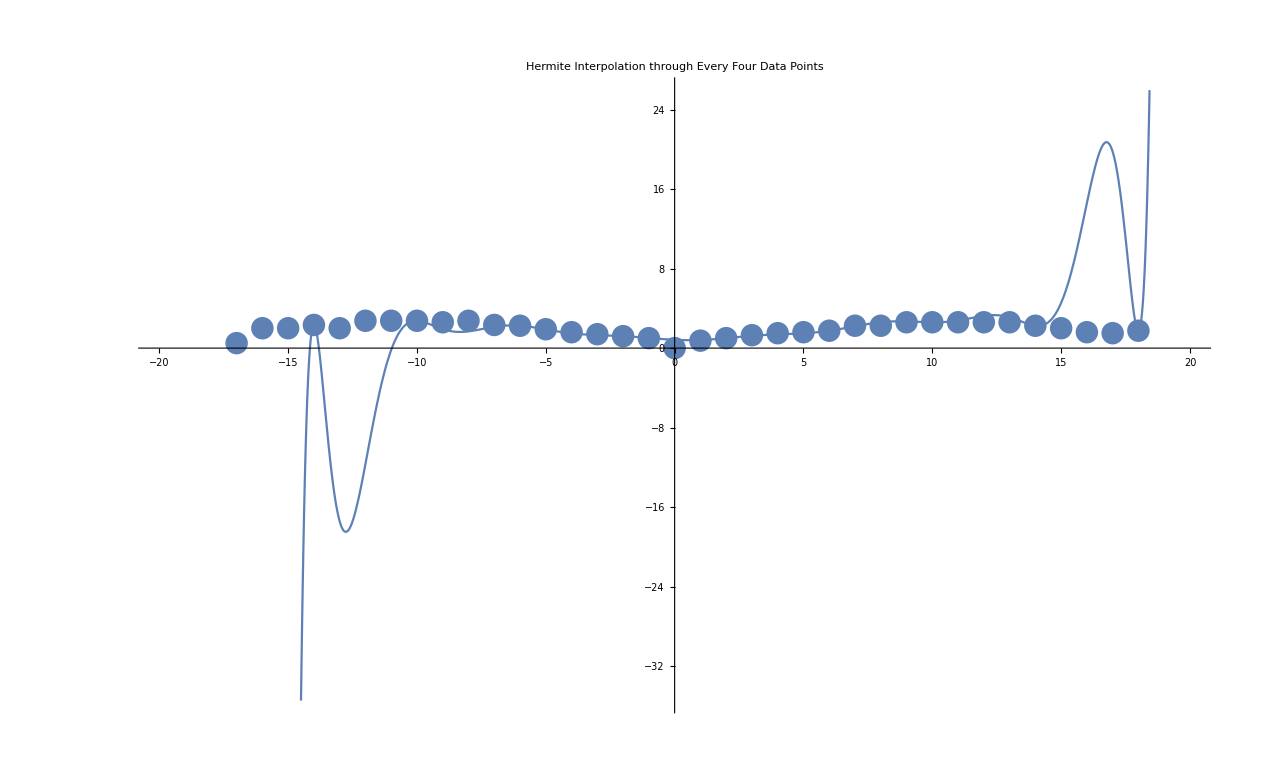

```mathematica
Show[
Plot[Herm[x],{x,-20,20}, PlotLabel-> "Hermite Interpolation through Every Four Data Points"],
ListPlot[OrderedPairs]
]
```

## Cubic Spline Interpolation

```mathematica
d= Length[xi];
hi = Table[{}, Length[xi]-1];
For[i=1, i≤ Length[xi]-1,i++,
hi[[i]] = xi[[i+1]]-xi[[i]]]
hi
aMatrix = Table[{},d-2,d-2];
MatrixForm[aMatrix];

For[ j=1,j≤ d-2, j++,
For[i=1,i≤ d-2, i++,
aMatrix[[i,j]] = 0
]
]

(*First diagonal (i)*)
For[ j=2,j≤ d-2, j++,
For[i=j-1,i≤ j-1, i++,
aMatrix[[i,j]] = hi[[i+1]]
]
]

(*Middle diagonal (i)*)
For[ j=1,j≤ d-2, j++,
For[i=j,i≤ j, i++,
aMatrix[[i,j]] = (2(hi[[i]]+hi[[i+1]]))
]
]
(*Bottom Diagonal (i-1)*)
For[ j=1,j≤ d-3, j++,
For[i=j+1,i≤ j+1, i++,
aMatrix[[i,j]] = hi[[i]]
]
]


(*Matrix A to solve for cj*)
MatrixForm[aMatrix]

(*Matrix b to solve for cj's*)
bMatrix = Table[{},d-2,1];
For[i=2,i≤ d-1, i++,
bMatrix[[i-1]] = ((3/hi[[i]])(fxi[[i+1]]-fxi[[i]]))-((3/hi[[i-1]])(fxi[[i]]-fxi[[i-1]]))
]
bMatrix

(*Correct Matrix for b*)
MatrixForm[bMatrix]
cj=LinearSolve[aMatrix,bMatrix]
(*Do not redo this Function or else to many variables in cj*)
PrependTo[cj,0];
AppendTo[cj,0];
cj
(*Creating the bj Mat*)
bj = Table[{},d-1,1];
MatrixForm[bj];
(*Filling bj matrix with proper values*)
For[i=1,i≤d-1, i++,
bj[[i]] = ((fxi[[i+1]]-fxi[[i]])/hi[[i]])-((hi[[i]]/3)(2cj[[i]]+cj[[i+1]]))
]
bj
(*Making a Matrix for dj*)
dj = Table[{},d-1,1];
MatrixForm[dj]
For[i=1,i≤d-1, i++,
dj[[i]] = (1/(3hi[[i]]))(cj[[i+1]]-cj[[i]])
]
dj
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

(4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4)

{-4.5,0.99,-1.98,3.24,-2.25,0.,-0.45,0.9,-1.71,1.02,-0.81,0.15,0.3,6.66134×10^-16,0.,-2.4,5.25,-1.5,0.15,-0.3,-0.3,0.15,1.05,-1.5,1.05,-1.05,0.,0.,0.,-1.05,0.3,-0.45,0.9,1.05}

(-4.5
0.99
-1.98
3.24
-2.25
0.
-0.45
0.9
-1.71
1.02
-0.81
0.15
0.3
6.66134×10^-16
0.
-2.4
5.25
-1.5
0.15
-0.3
-0.3
0.15
1.05
-1.5
1.05
-1.05
0.
0.
0.
-1.05
0.3
-0.45
0.9
1.05)

{-1.33483,0.839334,-1.0325,1.31067,-0.970197,0.320114,-0.31026,0.470927,-0.673448,0.512864,-0.358008,0.109169,0.0713322,-0.0944979,0.306659,-1.13214,1.8219,-0.90546,0.299942,-0.144307,-0.0227143,-0.0648359,0.432058,-0.613396,0.521527,-0.422712,0.119322,-0.0545743,0.0989756,-0.341328,0.216337,-0.224019,0.229738,0.205065}

{0,-1.33483,0.839334,-1.0325,1.31067,-0.970197,0.320114,-0.31026,0.470927,-0.673448,0.512864,-0.358008,0.109169,0.0713322,-0.0944979,0.306659,-1.13214,1.8219,-0.90546,0.299942,-0.144307,-0.0227143,-0.0648359,0.432058,-0.613396,0.521527,-0.422712,0.119322,-0.0545743,0.0989756,-0.341328,0.216337,-0.224019,0.229738,0.205065,0}

{1.94494,0.610111,0.114611,-0.0785568,0.199616,0.540093,-0.109989,-0.100135,0.0605312,-0.141989,-0.302573,-0.147718,-0.396557,-0.216056,-0.239221,-0.0270597,-0.85254,-0.16278,0.75366,0.148141,0.303776,0.136755,0.0492046,0.416427,0.235088,0.143219,0.242034,-0.0613563,0.003391,0.0477923,-0.19456,-0.319552,-0.327234,-0.321514,0.11329}

({}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{})

{-0.444944,0.724722,-0.623945,0.781059,-0.760291,0.430104,-0.210125,0.260396,-0.381458,0.395437,-0.290291,0.155726,-0.0126123,-0.0552767,0.133719,-0.4796,0.98468,-0.90912,0.401801,-0.148083,0.0405309,-0.0140405,0.165631,-0.348485,0.378308,-0.314746,0.180678,-0.0579653,0.0511833,-0.146768,0.185888,-0.146785,0.151252,-0.00822431,-0.0683551}

```mathematica
Remove[Wild]

Wild[x_] := Piecewise[ {
{fxi[[1]] + bj[[1]](x-xi[[1]])+ cj[[1]](x-xi[[1]])^2 + dj[[1]](x-xi[[1]])^3, xi[[1]] ≤ x ≤ xi[[2]]},
{fxi[[2]] + bj[[2]](x-xi[[2]])+ cj[[2]](x-xi[[2]])^2 + dj[[2]](x-xi[[2]])^3,  xi[[2]] ≤ x ≤ xi[[3]]},
{fxi[[3]] + bj[[3]](x-xi[[3]])+ cj[[3]](x-xi[[3]])^2 + dj[[3]](x-xi[[3]])^3,  xi[[3]] ≤ x ≤ xi[[4]]},
{fxi[[4]] + bj[[4]](x-xi[[4]])+ cj[[4]](x-xi[[4]])^2 + dj[[4]](x-xi[[4]])^3,  xi[[4]] ≤ x ≤ xi[[5]]},
{fxi[[5]] + bj[[5]](x-xi[[5]])+ cj[[5]](x-xi[[5]])^2 + dj[[5]](x-xi[[5]])^3,  xi[[5]] ≤ x ≤ xi[[6]]},
{fxi[[6]] + bj[[6]](x-xi[[6]])+ cj[[6]](x-xi[[6]])^2 + dj[[6]](x-xi[[6]])^3,  xi[[6]] ≤ x ≤ xi[[7]]},
{fxi[[7]] + bj[[7]](x-xi[[7]])+ cj[[7]](x-xi[[7]])^2 + dj[[7]](x-xi[[7]])^3,  xi[[7]] ≤ x ≤ xi[[8]]},
{fxi[[8]] + bj[[8]](x-xi[[8]])+ cj[[8]](x-xi[[8]])^2 + dj[[8]](x-xi[[8]])^3,  xi[[8]] ≤ x ≤ xi[[9]]},
{fxi[[9]] + bj[[9]](x-xi[[9]])+ cj[[9]](x-xi[[9]])^2 + dj[[9]](x-xi[[9]])^3,  xi[[9]] ≤ x ≤ xi[[10]]},
{fxi[[10]] + bj[[10]](x-xi[[10]])+ cj[[10]](x-xi[[10]])^2 + dj[[10]](x-xi[[10]])^3,  xi[[10]] ≤ x ≤ xi[[11]]},
{fxi[[11]] + bj[[11]](x-xi[[11]])+ cj[[11]](x-xi[[11]])^2 + dj[[11]](x-xi[[11]])^3, xi[[11]] ≤ x ≤ xi[[12]]},
{fxi[[12]] + bj[[12]](x-xi[[12]])+ cj[[12]](x-xi[[12]])^2 + dj[[12]](x-xi[[12]])^3,  xi[[12]] ≤ x ≤ xi[[13]]},
{fxi[[13]] + bj[[13]](x-xi[[13]])+ cj[[13]](x-xi[[13]])^2 + dj[[13]](x-xi[[13]])^3,  xi[[13]] ≤ x ≤ xi[[14]]},
{fxi[[14]] + bj[[14]](x-xi[[14]])+ cj[[14]](x-xi[[14]])^2 + dj[[14]](x-xi[[14]])^3,  xi[[14]] ≤ x ≤ xi[[15]]},
{fxi[[15]] + bj[[15]](x-xi[[15]])+ cj[[15]](x-xi[[15]])^2 + dj[[15]](x-xi[[15]])^3,  xi[[15]] ≤ x ≤ xi[[16]]},
{fxi[[16]] + bj[[16]](x-xi[[16]])+ cj[[16]](x-xi[[16]])^2 + dj[[16]](x-xi[[16]])^3,  xi[[16]] ≤ x ≤ xi[[17]]},
{fxi[[17]] + bj[[17]](x-xi[[17]])+ cj[[17]](x-xi[[17]])^2 + dj[[17]](x-xi[[17]])^3,  xi[[17]] ≤ x ≤ xi[[18]]},
{fxi[[18]] + bj[[18]](x-xi[[18]])+ cj[[18]](x-xi[[18]])^2 + dj[[18]](x-xi[[18]])^3,  xi[[18]] ≤ x ≤ xi[[19]]},
{fxi[[19]] + bj[[19]](x-xi[[19]])+ cj[[19]](x-xi[[19]])^2 + dj[[19]](x-xi[[19]])^3,  xi[[19]] ≤ x ≤ xi[[20]]},
{fxi[[20]] + bj[[20]](x-xi[[20]])+ cj[[20]](x-xi[[20]])^2 + dj[[20]](x-xi[[20]])^3,  xi[[20]] ≤ x ≤ xi[[21]]},
{fxi[[21]] + bj[[21]](x-xi[[21]])+ cj[[21]](x-xi[[21]])^2 + dj[[21]](x-xi[[21]])^3, xi[[21]] ≤ x ≤ xi[[22]]},
{fxi[[22]] + bj[[22]](x-xi[[22]])+ cj[[22]](x-xi[[22]])^2 + dj[[22]](x-xi[[22]])^3,  xi[[22]] ≤ x ≤ xi[[23]]},
{fxi[[23]] + bj[[23]](x-xi[[23]])+ cj[[23]](x-xi[[23]])^2 + dj[[23]](x-xi[[23]])^3,  xi[[23]] ≤ x ≤ xi[[24]]},
{fxi[[24]] + bj[[24]](x-xi[[24]])+ cj[[24]](x-xi[[24]])^2 + dj[[24]](x-xi[[24]])^3,  xi[[24]] ≤ x ≤ xi[[25]]},
{fxi[[25]] + bj[[25]](x-xi[[25]])+ cj[[25]](x-xi[[25]])^2 + dj[[25]](x-xi[[25]])^3,  xi[[25]] ≤ x ≤ xi[[26]]},
{fxi[[26]] + bj[[26]](x-xi[[26]])+ cj[[26]](x-xi[[26]])^2 + dj[[26]](x-xi[[26]])^3,  xi[[26]] ≤ x ≤ xi[[27]]},
{fxi[[27]] + bj[[27]](x-xi[[27]])+ cj[[27]](x-xi[[27]])^2 + dj[[27]](x-xi[[27]])^3,  xi[[27]] ≤ x ≤ xi[[28]]},
{fxi[[28]] + bj[[28]](x-xi[[28]])+ cj[[28]](x-xi[[28]])^2 + dj[[28]](x-xi[[28]])^3,  xi[[28]] ≤ x ≤ xi[[29]]},
{fxi[[29]] + bj[[29]](x-xi[[29]])+ cj[[29]](x-xi[[29]])^2 + dj[[29]](x-xi[[29]])^3,  xi[[29]] ≤ x ≤ xi[[30]]},
{fxi[[30]] + bj[[30]](x-xi[[30]])+ cj[[30]](x-xi[[30]])^2 + dj[[30]](x-xi[[30]])^3,  xi[[30]] ≤ x ≤ xi[[31]]},
{fxi[[31]] + bj[[31]](x-xi[[31]])+ cj[[31]](x-xi[[31]])^2 + dj[[31]](x-xi[[31]])^3,  xi[[31]] ≤ x ≤ xi[[32]]},
{fxi[[32]] + bj[[32]](x-xi[[32]])+ cj[[32]](x-xi[[32]])^2 + dj[[32]](x-xi[[32]])^3,  xi[[32]] ≤ x ≤ xi[[33]]},
{fxi[[33]] + bj[[33]](x-xi[[33]])+ cj[[33]](x-xi[[33]])^2 + dj[[33]](x-xi[[33]])^3,  xi[[33]] ≤ x ≤ xi[[34]]},
{fxi[[34]] + bj[[34]](x-xi[[34]])+ cj[[34]](x-xi[[34]])^2 + dj[[34]](x-xi[[34]])^3,  xi[[34]] ≤ x ≤ xi[[35]]},
{fxi[[35]] + bj[[35]](x-xi[[35]])+ cj[[35]](x-xi[[35]])^2 + dj[[35]](x-xi[[35]])^3,  xi[[35]] ≤ x ≤ xi[[36]]}
}]
```

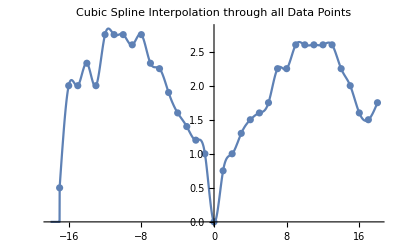

```mathematica
Show[
Plot[Wild[x],{x,-18,18}, PlotLabel-> "Cubic Spline Interpolation through all Data Points"],
ListPlot[OrderedPairs]
]
```

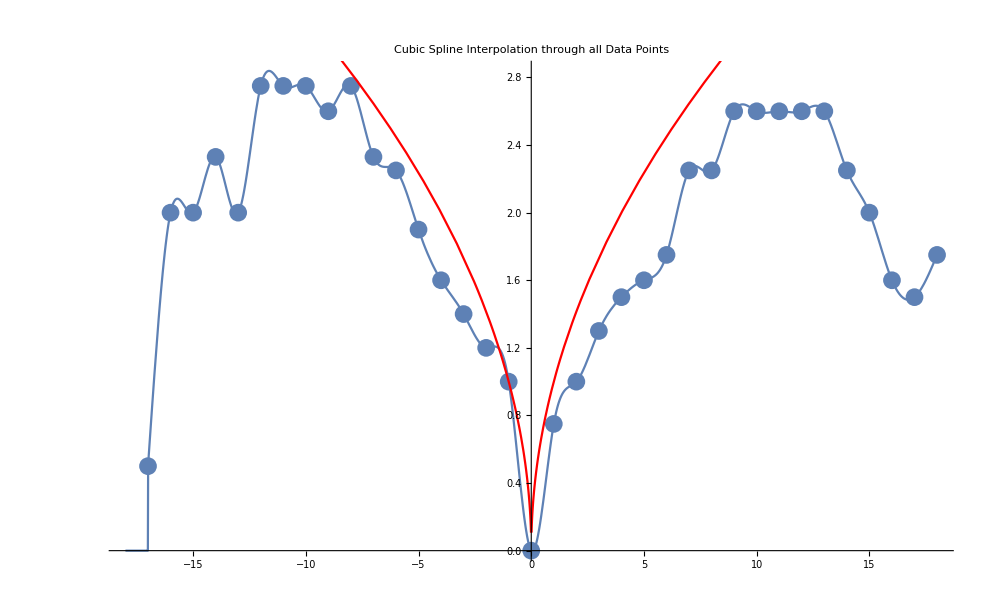

```mathematica
Show[
Plot[Wild[x],{x,-18,18}, PlotLabel-> "Cubic Spline Interpolation through all Data Points"],
ListPlot[OrderedPairs],
Plot[f[x],{x,-18,18}, PlotStyle->Red]
]
```

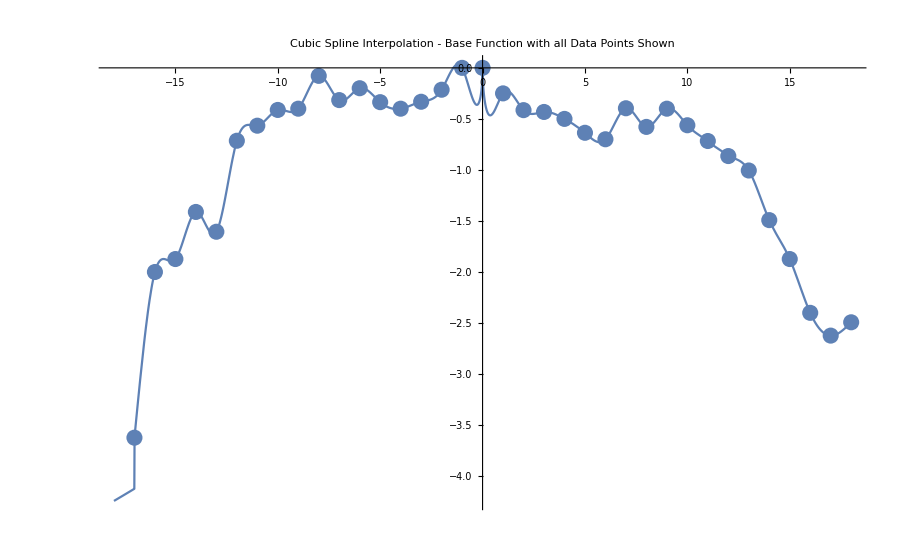

```mathematica
Show[
Plot[Wild[x]-f[x],{x,-18,18}, PlotLabel-> "Cubic Spline Interpolation - Base Function with all Data Points Shown"],
ListPlot[OrderedPairs3]
]
```

```mathematica
error = Table[{}, n];
For[i = 1, i≤ n, i++,
error[[i]] = Wild[xi[[i]]]-f[xi[[i]]]]
error
```

{-3.62311,-2.,-1.87298,-1.41166,-1.60555,-0.714102,-0.566625,-0.412278,-0.4,-0.0784271,-0.315751,-0.19949,-0.336068,-0.4,-0.332051,-0.214214,0.,-1.11022×10^-16,-0.25,-0.414214,-0.432051,-0.5,-0.636068,-0.69949,-0.395751,-0.578427,-0.4,-0.562278,-0.716625,-0.864102,-1.00555,-1.49166,-1.87298,-2.4,-2.62311,-2.49264}

```mathematica
OrderedPairs3 = Table[{}, n];
For[ i=1, i ≤ n, i++,
OrderedPairs3[[i]] = {xi[[i]],error[[i]]}
]
OrderedPairs3
```

{{-17,-3.62311},{-16,-2.},{-15,-1.87298},{-14,-1.41166},{-13,-1.60555},{-12,-0.714102},{-11,-0.566625},{-10,-0.412278},{-9,-0.4},{-8,-0.0784271},{-7,-0.315751},{-6,-0.19949},{-5,-0.336068},{-4,-0.4},{-3,-0.332051},{-2,-0.214214},{-1,0.},{0,-1.11022×10^-16},{1,-0.25},{2,-0.414214},{3,-0.432051},{4,-0.5},{5,-0.636068},{6,-0.69949},{7,-0.395751},{8,-0.578427},{9,-0.4},{10,-0.562278},{11,-0.716625},{12,-0.864102},{13,-1.00555},{14,-1.49166},{15,-1.87298},{16,-2.4},{17,-2.62311},{18,-2.49264}}

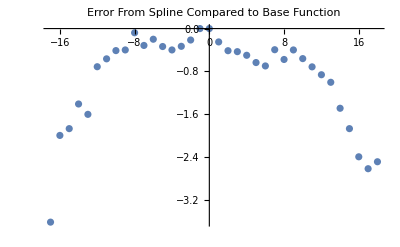

```mathematica
ListPlot[OrderedPairs3, PlotLabel->"Error From Spline Compared to Base Function"]
```